Pruebas y condicionales

¿Es 2+2 igual a 4? Se le pregunta a Wolfram Language.

Compruebe si 2+2 es igual a 4:

```mathematica
2+2==4
```

True

No es de sorprender que al comprobar si 2+2 es igual a 4, el resultado sea True (que significa verdadero en inglés).

Puede comprobarse también si 2×2 es mayor que 5. Para ese propósito se usa >.

Compruebe si 2×2 es mayor que 5:

```mathematica
2*2>5
```

False

La función If permite elegir un resultado cuando una comprobación da True, y otro cuando da False.

Puesto que la comprobación da True, el resultado del If es x:

```mathematica
If[2+2==4,x,y]
```

x

Si se usa una función pura con /@, puede aplicarse un If a cada elemento de una lista.

Si un elemento es menor que 4, hacerlo x, de lo contrario hacerlo y:

```mathematica
If[#<4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,y,y,y,y}

Puede hacerse la comprobación para menor o igual usando ≤, lo que se escribe como <=.

Si un elemento es menor o igual a 4, hágalo x; de lo contrario, hágalo y:

```mathematica
If[#≤ 4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,x,y,y,y}

En lo que sigue, un elemento se hace x solo si es igual a 4:

```mathematica
If[#== 4,x,y]&/@{1,2,3,4,5,6,7}
```

{y,y,y,x,y,y,y}

Puede hacerse la comprobación de que dos cosas no sean iguales usando ≠, lo que se escribe como !=.

Si un elemento no es igual a 4, hacerlo x; de lo contrario, hacerlo y:

```mathematica
If[#≠ 4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,y,x,x,x}

A veces es útil seleccionar aquellos elementos de una lista que satisfagan un criterio. Esto se hace usando Select, estableciendo dicha comprobación en términos de una función pura.

Seleccione los elementos de la lista que sean mayores que 3:

```mathematica
Select[{1,2,3,4,5,6,7},#>3&]
```

{4,5,6,7}

Seleccione los elementos que estén entre 2 y 5:

```mathematica
Select[{1,2,3,4,5,6,7},2≤#≤5&]
```

{2,3,4,5}

Además de las comparaciones de tamaño tales como <, > y ==, Wolfram Language incluye muchos otros tipos de pruebas. Algunos ejemplos son EvenQ y OddQ, que comprueban si un número es par o impar. (La “Q” indica que una función está formulando una pregunta).

4 es un número par:

```mathematica
EvenQ[4]
```

True

Seleccione de la lista los números pares:

```mathematica
Select[{1,2,3,4,5,6,7,8,9},EvenQ[#]&]
```

{2,4,6,8}

En este caso no es necesario que la función pura se haga explícita:

```mathematica
Select[{1,2,3,4,5,6,7,8,9},EvenQ]
```

{2,4,6,8}

IntegerQ comprueba si algo es un entero; PrimeQ comprueba si un número es primo.

Seleccione los números primos:

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10},PrimeQ]
```

{2,3,5,7}

A veces se necesita combinar comprobaciones. && representa “y”, || representa “o” y ! representa “no”.

Seleccione los elementos de la lista que sean a la vez pares y mayores que 2:

```mathematica
Select[{1,2,3,4,5,6,7},EvenQ[#]&&#>2&]
```

{4,6}

Seleccione los elementos que sean pares o mayores que 4:

```mathematica
Select[{1,2,3,4,5,6,7},EvenQ[#]||#>4&]
```

{2,4,5,6,7}

Seleccione los elementos que no sean pares o mayores que 4:

```mathematica
Select[{1,2,3,4,5,6,7},!(EvenQ[#]||#>4)&]
```

{1,3}

Hay muchas otras “funciones Q” que formulan preguntas sobre diversos tipos de cosas. LetterQ comprueba si una cadena de caracteres está compuesta solo de letras.

El espacio entre letras no es una letra, ni tampoco lo es “!”:

```mathematica
{LetterQ["a"],LetterQ["bc"],LetterQ["a b"],LetterQ["!"]}
```

{True,True,False,False}

Convierta una cadena en una lista de caracteres, y compruebe cuáles de ellos son letras:

```mathematica
LetterQ/@Characters["30 is the best!"]
```

{False,False,False,True,True,False,True,True,True,False,True,True,True,True,False}

Seleccione los caracteres que sean letras:

```mathematica
Select[Characters["30 is the best!"],LetterQ]
```

{i,s,t,h,e,b,e,s,t}

Seleccione las letras que estén después de la posición 10 en el alfabeto inglés:

```mathematica
Select[Characters["30 is the best!"],LetterQ[#]&&LetterNumber[#]>10&]
```

{s,t,s,t}

Puede usarse Select para encontrar palabras en inglés que sean palíndromos, esto es, que se lean igual si se invierte el orden de sus letras.

```mathematica
Select[WordList[ ],StringReverse[#]==#&]
```

{a,aha,bib,bob,boob,civic,dad,deed,dud,ere,eve,ewe,eye,gag,gig,huh,kayak,kook,level,ma'am,madam,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,refer,rotor,sis,tat,tenet,toot,tot,tut,wow}

MemberQ comprueba si alguna cosa aparece como un elemento de una lista o está contenido en ella.

5 aparece en la lista {1,3,5,7}:

```mathematica
MemberQ[{1,3,5,7},5]
```

True

Seleccione los números entre 1 y 100 cuyas secuencias de dígitos contengan el 2:

```mathematica
Select[Range[100],MemberQ[IntegerDigits[#],2]&]
```

{2,12,20,21,22,23,24,25,26,27,28,29,32,42,52,62,72,82,92}

ImageInstanceQ es una comprobación basada en el aprendizaje automático que comprueba si una imagen es un caso de algún tipo particular de algo como, por ejemplo, un gato.

Compruebe si una imagen es la de un gato:

```mathematica
ImageInstanceQ[-Graphics-,LinguisticAssistant]
```

True

Seleccione las imágenes que sean de gatos:

```mathematica
Select[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},ImageInstanceQ[#,LinguisticAssistant]&]
```

{-Graphics-,-Graphics-}

He aquí un ejemplo geográfico de Select: encuentre cuáles de las ciudades en una lista se ubican a menos de 3 000 millas de San Francisco.

Seleccione las ciudades cuya distancia a San Francisco sea menor de 3 000 millas:

```mathematica
Select[{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant},GeoDistance[#,LinguisticAssistant]<LinguisticAssistant&]
```

{New York City,Chicago}

Vocabulario

a==b |   | comprueba igualdad
a<b |   | comprueba si es menor que
a>b |   | comprueba si es mayor que
a≤b |   | comprueba si es menor o igual
a≥b |   | comprueba si es mayor o igual
If[test,u,v] |   | obtiene el resultado u si test es True y v si es False
Select[lista,f] |   | selecciona los elementos que satisfacen un criterio
EvenQ[x] |   | comprueba si es par
OddQ[x] |   | comprueba si es impar
IntegerQ[x] |   | comprueba si es un entero
PrimeQ[x] |   | comprueba si es un número primo
LetterQ[cadena] |   | comprueba si solo son letras
MemberQ[lista,x] |   | comprueba si x está contenido en lista
ImageInstanceQ[imagen,categoría] |   | comprueba si imagen es un caso de categoría

"13 Exercises Available"
"with 7 extras" | "Get Started »"

Compruebe si 123^321 es mayor que 456^123. »

| Expected output: |  
  | True |

Obtenga una lista de los números hasta el 100 cuyos dígitos sumen menos de 5. »

| Expected output: |  
  | {1,2,3,4,10,11,12,13,20,21,22,30,31,40,100} |

Haga una lista de los 20 primeros enteros, coloreando con rojo los que sean primos. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20} |

Encuentre las palabras en WordList[ ] que comiencen y terminen con la letra “p”. »

| Expected output: |  
  | {"pap","paperclip","parsnip","partisanship","partnership","pawnshop","payslip","peep","penmanship","pep","pickup","pileup","pimp","pip","plop","plump","polyp","pomp","poop","pop","premiership","prep","primp","professorship","prop","proprietorship","pulp","pump","pup"} |

Haga una lista de los 100 primeros primos, conservando aquellos cuyo último dígito sea menor que 3. »

| Expected output: |  
  | {2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541} |

Encuentre los números romanos hasta el 100 que no contengan “I”. »

| Expected output: |  
  | {"V","X","XV","XX","XXV","XXX","XXXV","XL","XLV","L","LV","LX","LXV","LXX","LXXV","LXXX","LXXXV","XC","XCV","C"} |

Obtenga la lista de los números romanos hasta el 1000 que sean palíndromos. »

| Expected output: |  
  | {"I","II","III","V","X","XIX","XX","XXX","L","C","CXC","CC","CCC","D","M"} |

Encuentre los nombres en inglés de los enteros hasta el 100 que comiencen y terminen con la misma letra. »

| Expected output: |  
  | {"nineteen","twenty-eight","thirty-eight","eighty-one","eighty-three","eighty-five","eighty-nine","ninety-seven"} |

Obtenga la lista de las palabras en el artículo de Wikipedia “words”, cuyo número de caracteres sea mayor de 15. »

| Sample expected output: |  
  | {"orthographically","multiple-morpheme","Proto-Indo-European"} |

A partir de 1000, divida entre 2 si el número es par y, en caso contrario, calcule 3#+1& ; repita esto 200 veces (problema de Collatz). »

| Expected output: |  
  | {1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2} |

Cree la nube de las palabras que tengan 5 letras en el artículo de Wikipedia sobre “computers”. »

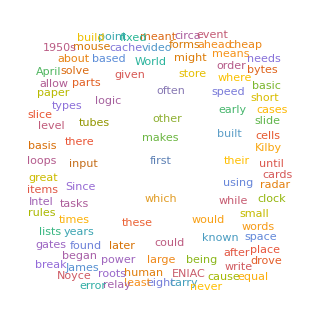
| Sample expected output: |  
  | -Graphics- |

Encuentre las palabras en WordList[ ] cuyas 3 primeras letras sean las mismas que sus 3 últimas en orden inverso, pero tales que la cadena completa de sus caracteres no sea un palíndromo. »

| Expected output: |  
  | {"despised","detected","detested","drainboard","foolproof","lackadaisical","marjoram","revolver"} |

Encuentre las palabras de 10 letras en WordList[ ] donde el total de los valores obtenidos con LetterNumber sea 100. »

| Expected output: |  
  | {"accumulate","alienation","answerable","apoplectic","aquamarine","bewitching","censurable","ceramicist","chastening","chimpanzee","clementine","clinically","collecting","condensate","congenital","conjugated","connivance","declension","deliquesce","demobilize","demodulate","denominate","diagonally","discipline","discommode","egoistical","emasculate","embodiment","emendation","empathetic","fatalistic","fatherhood","geographer","hemoglobin","impugnable","inadequacy","interbreed","leveraging","liberalism","likelihood","martingale","mercantile","meridional","neoclassic","paramecium","plebiscite","potbellied","quadrangle","reciprocal","regimented","reschedule","researcher","scoreboard","septicemia","shibboleth","sleepyhead","stagecraft","stalemated","temperance","thickening","threatened","uncombined","unmodified"} |

Haga una lista de los enteros hasta el 25, donde cada entero que termine en 3 se reemplace por 0. »

| Expected output: |  
  | {1,2,0,4,5,6,7,8,9,10,11,12,0,14,15,16,17,18,19,20,21,22,0,24,25} |

Use Table e If para hacer un arreglo de 5×5 que tenga 1 en su diagonal principal, y 0 fuera de ahí.  »

| Expected output: |  
  | {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} |

Haga una lista de los números hasta el 1000 que sean a la vez iguales a 1 mod 7 y a 1 mod 8. »

| Expected output: |  
  | {1,57,113,169,225,281,337,393,449,505,561,617,673,729,785,841,897,953} |

Haga una lista de los números hasta el 100, en la que los múltiplos de 3 se reemplacen por Black, los que sean múltiplos de 5 se reemplacen por White y los que sean a la vez múltiplos de 3 y de 5 se reemplacen por Red. »

| Expected output: |  
  | {1,2,GrayLevel[0],4,GrayLevel[1],GrayLevel[0],7,8,GrayLevel[0],GrayLevel[1],11,GrayLevel[0],13,14,RGBColor[1, 0, 0],16,17,GrayLevel[0],19,GrayLevel[1],GrayLevel[0],22,23,GrayLevel[0],GrayLevel[1],26,GrayLevel[0],28,29,RGBColor[1, 0, 0],31,32,GrayLevel[0],34,GrayLevel[1],GrayLevel[0],37,38,GrayLevel[0],GrayLevel[1],41,GrayLevel[0],43,44,RGBColor[1, 0, 0],46,47,GrayLevel[0],49,GrayLevel[1],GrayLevel[0],52,53,GrayLevel[0],GrayLevel[1],56,GrayLevel[0],58,59,RGBColor[1, 0, 0],61,62,GrayLevel[0],64,GrayLevel[1],GrayLevel[0],67,68,GrayLevel[0],GrayLevel[1],71,GrayLevel[0],73,74,RGBColor[1, 0, 0],76,77,GrayLevel[0],79,GrayLevel[1],GrayLevel[0],82,83,GrayLevel[0],GrayLevel[1],86,GrayLevel[0],88,89,RGBColor[1, 0, 0],91,92,GrayLevel[0],94,GrayLevel[1],GrayLevel[0],97,98,GrayLevel[0],GrayLevel[1]} |

Use Select para obtener la lista de los planetas cuya masa sea mayor que la de la Tierra. »

| Expected output: |  
  | {"Jupiter","Saturn","Uranus","Neptune"} |

Haga un gráfico de arreglo 50×50 donde haya un cuadrado negro en la posición i,j si Mod[i,j]==0. »

| Expected output: |  
  | -Graphics- |

Haga un gráfico de arreglo de 100×100, donde un cuadrado sea negro si los dos valores de sus posiciones x y y no contienen un 5. »

| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Por qué la igualdad se comprueba con == y no con =?

Porque en Wolfram Language = significa otra cosa. Si por error se usa = en vez de == , se obtendrán resultados muy extraños. (= es para asignar valores a variables.) Para evitar posibles confusiones, suele leerse == como “doble signo de igual”.

¿Por qué “and” se escribe como &&, y no como &?

Porque & significa otra cosa en Wolfram Language. Por ejemplo, se usa para indicar dónde termina una función pura.

¿Cómo se interpretan ==, >, &&, etc. ?

== es Equal, ≠ (!=) es Unequal, > es Greater, ≥ es GreaterEqual, < es Less, && es And, || es Or y ! es Not.

¿En qué casos se requiere usar paréntesis al usar &&, ||, etc.?

Hay un orden en las operaciones que es directamente análogo al de la aritmética. && es como ×, || es como +, y ! es como −. Entonces, !p&&q significa “(no p) y q”; !(p&&q) significa “no (p y q)”.

¿Qué tienen de especial las funciones “Q”?

Hacen una pregunta que normalmente tiene como respuesta True o False.

¿Qué otras funciones “Q” existen?

NumberQ, StringContainsQ, BusinessDayQ y ConnectedGraphQ, entre otras.

¿Hay alguna forma mejor que Select para encontrar entidades del mundo real que tengan alguna propiedad dada?

Sí. Se pueden hacer cosas como Entity["Country","Population"→GreaterThan[10^7 "people"]] para encontrar “entidades implícitas”, y usar luego EntityList para obtener listas explícitas de entidades.

Notas técnicas

True y False se llaman típicamente booleanos en las ciencias de la computación (por George Boole, a mediados de los años 1800s). Las expresiones con &&, ||, etc. se suelen llamar expresiones booleanas.

En Wolfram Language, True y False son símbolos, y no están representadas por 1 y 0, como sucede en muchos otros lenguajes de computación.

If se suele llamar una condicional. En If[test,then,else], el then y else no se calculan a menos que test diga que la condición se cumple.

PalindromeQ prueba directamente si una cadena de caracteres forma un palíndromo.

En Wolfram Language, x es un símbolo (ver la Sección 33) que puede representar cualquier cosa, así que x==1 es simplemente una ecuación, que no es inmediatamente True o False. x===1 (“triple igual”) prueba si x es “lo mismo” que 1, y puesto que no lo es, da False.

Para explorar más

Guía para funciones que aplican pruebas en Wolfram Language »

Guía para computación Booleana en Wolfram Language »